# Transfer Fit of MC Data

```mathematica
MCFolder="~/ClusterMC_v4/NoMoS_Danfysik_25-02-19_reduceTypes_smallerDV4/";
```

```mathematica
DetHisto=Import[MCFolder<>"GlobalTransferData/"<>"DetXYHistSum.txt","Table"];
```

```mathematica
ListPlot3D[Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,1]]-DetHisto[[1,2]])/2,
DetHisto[[2,j]]+(DetHisto[[2,1]]-DetHisto[[2,2]])/2,
DetHisto[[2+i,j]]},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}
],1],PlotRange->All]
```

-Graphics3D-

### boolean plot to see, where > 0

```mathematica
ListPlot3D[Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,1]]-DetHisto[[1,2]])/2,
DetHisto[[2,j]]+(DetHisto[[2,1]]-DetHisto[[2,2]])/2,
Boole[DetHisto[[2+i,j]]>0]},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}
],1],PlotRange->All]
```

-Graphics3D-

```mathematica
{{ApertXOff,ApertYOff},{ApertX,ApertY},{BDV},{BF},{BA},{BRxB},{BDet}}=Import[MCFolder<>"GlobalTransferData/"<>"OtherParas.txt","Table"]
```

{{0.0301277,1.00623},{0.01,0.035},{0.220899},{0.451107},{0.219769},{0.219722},{0.207816}}

```mathematica
rF=BF/BDV
```

2.04214

```mathematica
rA=BA/BDV
```

0.994887

```mathematica
rRxB=BRxB/BDV
```

0.994674

```mathematica
rDet=BDet/BRxB
```

0.945816

### grab alpha from blines

```mathematica
AlphaFromBlines=178.24701452514864;
```

```mathematica
BRxBCenterFromBLines=0.21957007943037976;
```

```mathematica
(BRxBCenterFromBLines-BRxB)/BRxBCenterFromBLines
```

-0.000691704

### difference is 7e-4. as the MC value is the average over all particles, it doesnt represent the model description. Model needs BRxB in geometric center of beam (actually geometric tube)

### actually, thDet is also different due to alpha not doing 180°!

```mathematica
InfoFile=Import[MCFolder<>"info.txt","Table"];
```

```mathematica
R=InfoFile[[1,2]]
```

0.999002

### also, we havent considered a shift at detector due to field lines shifting..

## Get the transfer function

```mathematica
SetDirectory["~/eclipse-workspace/TransportProject/"]
```

/home/dmoser/eclipse-workspace/TransportProject

```mathematica
Get["NeutronBeam/NBeam_IntTables.m"]
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

Set::wrsym: Symbol pmax is Protected.

### calculate bins, choose binsize, multiple of MCData binning

### plot original grid

```mathematica
-(DetHisto[[1,1]]-DetHisto[[1,2]])
```

0.005

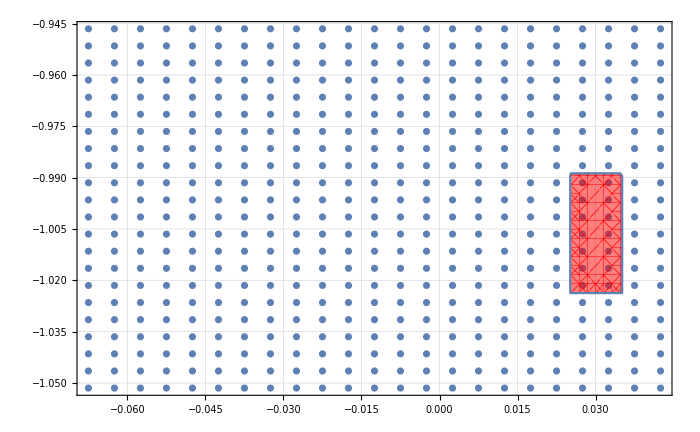

```mathematica
Show[
ListPlot[
Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,2]]-DetHisto[[1,1]])/2,
DetHisto[[2,j]]+(DetHisto[[2,2]]-DetHisto[[2,1]])/2
},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}],1],PlotRange->All],
RegionPlot[Abs[x-ApertXOff]<ApertX/2&&Abs[y+ApertYOff]<ApertY/2,{x,0,0.06},{y,-1.05,-0.95},PlotStyle->Directive[Red,Opacity[0.5]]]
]
```

```mathematica
?XYBinIntBoundaries
```

### we can directly get a XYBin form from original table, even being able to jump over steps by 2 e.g.

```mathematica
XYBinBoundariesOriginal=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{DetHisto[[2,yi]],DetHisto[[2,yi+1]]}
},{xi,1,Length[DetHisto[[1]]]-1},{yi,1,Length[DetHisto[[2]]]-1}],1];
```

```mathematica
XYBinBoundariesOriginal//Length
```

506

### half bins

```mathematica
XYBinBoundariesHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+2]]},
{DetHisto[[2,yi]],DetHisto[[2,yi+2]]}
},{xi,2,Length[DetHisto[[1]]]-1,2},{yi,1,Length[DetHisto[[2]]]-1,2}],1];
```

### we start for x at index 2 for shift, also because that area is 0 anyway

```mathematica
XYBinBoundariesHalf//Length
```

121

```mathematica
(506-22)/4.
```

121.

```mathematica
XYBinBoundariesHalf
```

{{{-0.065,-0.055},{-1.054,-1.044}},{{-0.065,-0.055},{-1.044,-1.034}},{{-0.065,-0.055},{-1.034,-1.024}},{{-0.065,-0.055},{-1.024,-1.014}},{{-0.065,-0.055},{-1.014,-1.004}},{{-0.065,-0.055},{-1.004,-0.994002}},{{-0.065,-0.055},{-0.994002,-0.984002}},{{-0.065,-0.055},{-0.984002,-0.974002}},{{-0.065,-0.055},{-0.974002,-0.964002}},{{-0.065,-0.055},{-0.964002,-0.954002}},{{-0.065,-0.055},{-0.954002,-0.944002}},{{-0.055,-0.045},{-1.054,-1.044}},{{-0.055,-0.045},{-1.044,-1.034}},{{-0.055,-0.045},{-1.034,-1.024}},{{-0.055,-0.045},{-1.024,-1.014}},{{-0.055,-0.045},{-1.014,-1.004}},{{-0.055,-0.045},{-1.004,-0.994002}},{{-0.055,-0.045},{-0.994002,-0.984002}},{{-0.055,-0.045},{-0.984002,-0.974002}},{{-0.055,-0.045},{-0.974002,-0.964002}},{{-0.055,-0.045},{-0.964002,-0.954002}},{{-0.055,-0.045},{-0.954002,-0.944002}},{{-0.045,-0.035},{-1.054,-1.044}},{{-0.045,-0.035},{-1.044,-1.034}},{{-0.045,-0.035},{-1.034,-1.024}},{{-0.045,-0.035},{-1.024,-1.014}},{{-0.045,-0.035},{-1.014,-1.004}},{{-0.045,-0.035},{-1.004,-0.994002}},{{-0.045,-0.035},{-0.994002,-0.984002}},{{-0.045,-0.035},{-0.984002,-0.974002}},{{-0.045,-0.035},{-0.974002,-0.964002}},{{-0.045,-0.035},{-0.964002,-0.954002}},{{-0.045,-0.035},{-0.954002,-0.944002}},{{-0.035,-0.025},{-1.054,-1.044}},{{-0.035,-0.025},{-1.044,-1.034}},{{-0.035,-0.025},{-1.034,-1.024}},{{-0.035,-0.025},{-1.024,-1.014}},{{-0.035,-0.025},{-1.014,-1.004}},{{-0.035,-0.025},{-1.004,-0.994002}},{{-0.035,-0.025},{-0.994002,-0.984002}},{{-0.035,-0.025},{-0.984002,-0.974002}},{{-0.035,-0.025},{-0.974002,-0.964002}},{{-0.035,-0.025},{-0.964002,-0.954002}},{{-0.035,-0.025},{-0.954002,-0.944002}},{{-0.025,-0.015},{-1.054,-1.044}},{{-0.025,-0.015},{-1.044,-1.034}},{{-0.025,-0.015},{-1.034,-1.024}},{{-0.025,-0.015},{-1.024,-1.014}},{{-0.025,-0.015},{-1.014,-1.004}},{{-0.025,-0.015},{-1.004,-0.994002}},{{-0.025,-0.015},{-0.994002,-0.984002}},{{-0.025,-0.015},{-0.984002,-0.974002}},{{-0.025,-0.015},{-0.974002,-0.964002}},{{-0.025,-0.015},{-0.964002,-0.954002}},{{-0.025,-0.015},{-0.954002,-0.944002}},{{-0.015,-0.005},{-1.054,-1.044}},{{-0.015,-0.005},{-1.044,-1.034}},{{-0.015,-0.005},{-1.034,-1.024}},{{-0.015,-0.005},{-1.024,-1.014}},{{-0.015,-0.005},{-1.014,-1.004}},{{-0.015,-0.005},{-1.004,-0.994002}},{{-0.015,-0.005},{-0.994002,-0.984002}},{{-0.015,-0.005},{-0.984002,-0.974002}},{{-0.015,-0.005},{-0.974002,-0.964002}},{{-0.015,-0.005},{-0.964002,-0.954002}},{{-0.015,-0.005},{-0.954002,-0.944002}},{{-0.005,0.005},{-1.054,-1.044}},{{-0.005,0.005},{-1.044,-1.034}},{{-0.005,0.005},{-1.034,-1.024}},{{-0.005,0.005},{-1.024,-1.014}},{{-0.005,0.005},{-1.014,-1.004}},{{-0.005,0.005},{-1.004,-0.994002}},{{-0.005,0.005},{-0.994002,-0.984002}},{{-0.005,0.005},{-0.984002,-0.974002}},{{-0.005,0.005},{-0.974002,-0.964002}},{{-0.005,0.005},{-0.964002,-0.954002}},{{-0.005,0.005},{-0.954002,-0.944002}},{{0.005,0.015},{-1.054,-1.044}},{{0.005,0.015},{-1.044,-1.034}},{{0.005,0.015},{-1.034,-1.024}},{{0.005,0.015},{-1.024,-1.014}},{{0.005,0.015},{-1.014,-1.004}},{{0.005,0.015},{-1.004,-0.994002}},{{0.005,0.015},{-0.994002,-0.984002}},{{0.005,0.015},{-0.984002,-0.974002}},{{0.005,0.015},{-0.974002,-0.964002}},{{0.005,0.015},{-0.964002,-0.954002}},{{0.005,0.015},{-0.954002,-0.944002}},{{0.015,0.025},{-1.054,-1.044}},{{0.015,0.025},{-1.044,-1.034}},{{0.015,0.025},{-1.034,-1.024}},{{0.015,0.025},{-1.024,-1.014}},{{0.015,0.025},{-1.014,-1.004}},{{0.015,0.025},{-1.004,-0.994002}},{{0.015,0.025},{-0.994002,-0.984002}},{{0.015,0.025},{-0.984002,-0.974002}},{{0.015,0.025},{-0.974002,-0.964002}},{{0.015,0.025},{-0.964002,-0.954002}},{{0.015,0.025},{-0.954002,-0.944002}},{{0.025,0.035},{-1.054,-1.044}},{{0.025,0.035},{-1.044,-1.034}},{{0.025,0.035},{-1.034,-1.024}},{{0.025,0.035},{-1.024,-1.014}},{{0.025,0.035},{-1.014,-1.004}},{{0.025,0.035},{-1.004,-0.994002}},{{0.025,0.035},{-0.994002,-0.984002}},{{0.025,0.035},{-0.984002,-0.974002}},{{0.025,0.035},{-0.974002,-0.964002}},{{0.025,0.035},{-0.964002,-0.954002}},{{0.025,0.035},{-0.954002,-0.944002}},{{0.035,0.045},{-1.054,-1.044}},{{0.035,0.045},{-1.044,-1.034}},{{0.035,0.045},{-1.034,-1.024}},{{0.035,0.045},{-1.024,-1.014}},{{0.035,0.045},{-1.014,-1.004}},{{0.035,0.045},{-1.004,-0.994002}},{{0.035,0.045},{-0.994002,-0.984002}},{{0.035,0.045},{-0.984002,-0.974002}},{{0.035,0.045},{-0.974002,-0.964002}},{{0.035,0.045},{-0.964002,-0.954002}},{{0.035,0.045},{-0.954002,-0.944002}}}

### calculate first transfer spectrum with the rough parameters

```mathematica
?BinInt
```

```mathematica
BinInt[0.,#,{AlphaFromBlines,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.03,0.},
{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,3,0,2},{IntOptionList[[6]],3,4}
]
```